## Pi4 Number Visibility

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
series=(1000#1+100#2+10#3+#4)&@@@Partition[RealDigits[Pi,10,40000][[1,2;;]],4];
```

## SDL Complexity

```mathematica
<<sdl.mx
```

```mathematica
sdl[series]
```

{0.140074,0.963661}

## Visibility

```mathematica
<<visibility.mx
```

```mathematica
links=naturalVisibilityLinks[series];
```

```mathematica
natGraph=Graph[links, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
count=VertexDegree[natGraph]//Counts
```

<|8→398,2→2279,9→310,4→1550,7→470,10→234,14→90,23→15,3→2026,6→721,5→983,15→64,12→159,11→207,19→32,32→5,17→53,22→24,37→3,16→62,24→13,29→4,35→1,25→17,28→11,40→1,13→137,18→44,26→5,20→30,30→4,33→5,31→7,34→2,50→1,21→19,27→9,39→2,43→1,1→1|>

```mathematica
If[count[1]<3,count[1]=.];
```

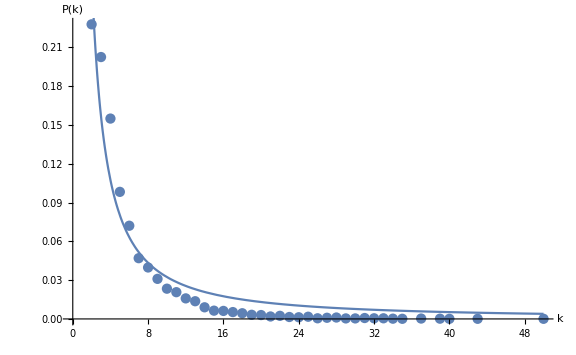
{{C→0.659701,γ→1.3088},-Graphics-}

```mathematica
plotModel[count,10000]
```

## Horizontal Visibility

```mathematica
horlinks=horizontalVisibilityLinks[series];
```

```mathematica
hg=Graph[horlinks, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
count=VertexDegree[hg]//Counts
```

<|5→900,2→3634,7→442,8→294,3→2155,4→1336,11→96,14→21,9→207,6→606,10→152,16→9,15→18,13→39,20→4,12→63,18→4,17→13,19→5,1→1|>

```mathematica
If[count[1]<3,count[1]=.];
```

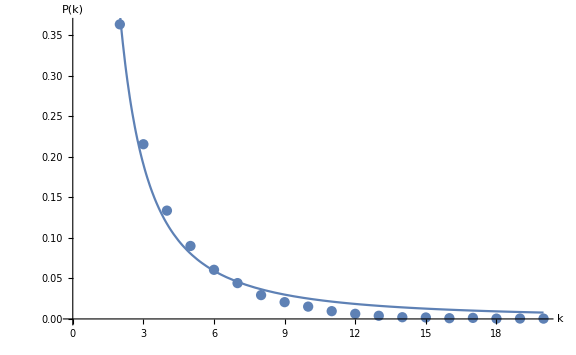
{{C→1.21138,γ→1.68331},-Graphics-}

```mathematica
plotModel[count,10000]
```